# Response Function- Deuteron 11/01/24

[σ_tot]=μb=10^-4 fm^2
[σ_tot]=mb=10^-1 fm^2
[Lab photon energy] = MeV

```mathematica
dbg=False;
```

#### set of regulator functions to smooth the discrete result of the inverse Lorentz transfrom

```mathematica
Off[Inverse::luc,General::munfl,FindFit::lstol,ClebschGordan::phy,LinearSolve::luc]
Needs["MaTeX`"]
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color,txfonts}"}];

readREAL8list[fn_,freal_:"Real64",finteger_:"Integer32"]:=Block[{str,headmarker,data},
str=OpenRead[fn,BinaryFormat->True];
headmarker=BinaryRead[str,finteger,ByteOrdering->$ByteOrdering];
data=BinaryReadList[str,freal,ByteOrdering->$ByteOrdering];
Close[str];
data];

trafoToIDNorm[normMat_]:=Block[{dbg=True},
{evaln,evecn}=Eigensystem[normMat];

diagev=DiagonalMatrix[evaln^(-0.5)];
fulltrafo=Transpose[evecn].diagev;
fulltrafo
];
```

```mathematica
multipolarity=1;
mLs=Range[-multipolarity,multipolarity,1];

parity="-";
Subscript[I, n]={0,1,2}; (*Spin of Excited states*)
J0=1; (*Spin of Ground states which consists of two channels s and d*)
mIns=Range[-#,#,1]&/@Subscript[I, n];
lege="J_lit="<>ToString[#]&/@Subscript[I, n];

dH=1; (* this takes only every dH basis vector into account; ECCE: not benchmarked *)
```

```mathematica
ImgSize=900;
mnucl=938.3;
hbarc=197.3269804; (*codata*)

hbarsqO2m=hbarc^2/(2 mnucl);
(*αfine=1./137.*)
αfine=UnitConvert[Quantity[1,"FineStructureConstant"]];
hat[l_]:=Sqrt[2 l+1];

(*resultsDir=$HomeDirectory<>"/kette_repo/LIT_source/systems/mul_deuteron_miwchan/results";*)
resultsDir="/home/kirscher/scratch/compton_IRS/miwchan/results"

files=FileNames[All,resultsDir];
anzBas=Length[Select[files,StringMatchQ[#,"*mat*BasNR*"]&]]/Length[Subscript[I, n]];

SetDirectory[resultsDir];
dt=ToString[Import["dtype.dat"][[1]][[1]]];
datatype="Real64";
Which[dt=="float32",datatype="Real32",dt=="float64",datatype="Real64"];
Print["Read FORTRAN results from \n",Style[resultsDir,18,Red],"\nin\n",Style[dt,18,Red],"=",Style[datatype,18,Red],"\nformat for\nN_bases=",Style[anzBas,18,Red],"\nevolved bases for the expansion of the final state."];
```

/home/kirscher/scratch/compton_IRS/miwchan/results

Read FORTRAN results from 
/home/kirscher/scratch/compton_IRS/miwchan/results
in
float32=Real32
format for
N_bases=1
evolved bases for the expansion of the final state.

"data" taken from https://arxiv.org/abs/1103.4434v1
the factor of 1.7 was observed in H. Arenhovel and M. Sanzone, Photodisintegration of the Deuteron

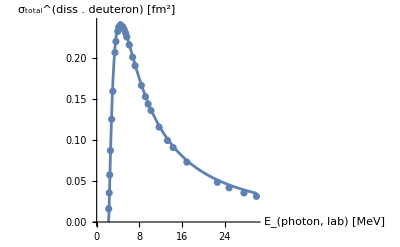

```mathematica
DDatamB=Import["/home/kirscher/kette_repo/LIT_source/data/D_photo_diss_E1.dat","Data"];
DDataFm2=Transpose[{Transpose[DDatamB][[1]],Transpose[DDatamB][[2]]}];
compensationFac=1.7;
σBethe[ω_,E0_,mM_]:=compensationFac (8 Pi)/3 1./137. 1./(mM E0) (ω/E0-1)^(3./2.)/(ω/E0)^3;
Show[
Plot[hbarc^2 σBethe[ν,2.22,938.],{ν,0,30},PlotRange->Full,AxesLabel->{"E_(photon, lab) [MeV]","σ_total^(diss . deuteron) [fm^2]"}],
ListPlot[DDataFm2,PlotLabel->Style["Analytical - E1",Orange,22]]]
```

### Read H_nm:=⟨n|(Ĥ)_(V18+UIX)|m⟩ and 𝕟_nm:=⟨n|OverHat[𝟙]|m⟩≠𝟙_nm

```mathematica
DNormHamMat=readREAL8list["./mat_np1^+"];
tmp=DNormHamMat[[Range[1,Length[DNormHamMat],2]]];

DBasisDim=IntegerPart[Sqrt[Length[DNormHamMat] 0.5]];
Print["Deuteron-basis Dimension = ",DBasisDim];

DNorm=ArrayReshape[DNormHamMat[[1;;DBasisDim^2]],{DBasisDim,DBasisDim}][[;;;;dH,;;;;dH]];
DHam=ArrayReshape[DNormHamMat[[DBasisDim^2+1;;]],{DBasisDim,DBasisDim}][[;;;;dH,;;;;dH]];
```

Deuteron-basis Dimension = 40

transform this basis s.t. one can safely “insert 𝟙”:

```mathematica
fulltrafonm=trafoToIDNorm[DNorm];

If[dbg,
Print[ArrayRules[SparseArray[Chop[Transpose[fulltrafonm].DNorm.fulltrafonm]]]];Print[fulltrafonm//MatrixForm];
Print[Chop[Transpose[fulltrafonm].DNorm.fulltrafonm]//MatrixForm];
Print[DNorm//MatrixForm];];
```

#### The initial state (Deuteron ground state D )

other parts of this section yield analytic information on the initial state

```mathematica
orderedEVDp=Sort[Transpose[Eigensystem[{DHam,DNorm}]],Re[#1[[1]]]<Re[#2[[1]]]&];
evalGSp=orderedEVDp[[1]][[1]]
evecGSp=orderedEVDp[[1]][[2]]
Norm[evecGSp]
orderedEVD=Sort[Transpose[Eigensystem[Transpose[fulltrafonm].DHam.fulltrafonm]],Re[#1[[1]]]<Re[#2[[1]]]&];
evalGS=orderedEVD[[1]][[1]]
evecGS=orderedEVD[[1]][[2]]
Norm[evecGS]
```

-2.21755

{0.0000335638,-0.000453311,0.00234248,-0.00769075,0.0194517,-0.0408488,0.0746842,-0.12234,0.182886,-0.252329,0.322951,-0.383472,0.420112,-0.420044,0.376339,-0.294027,0.192097,-0.0982831,0.034935,-0.00652552,-1.31709×10^-7,4.03245×10^-6,-6.52445×10^-6,-2.93238×10^-6,0.0000344755,-0.000120212,0.000265347,-0.000513112,0.000837446,-0.00125834,0.00171107,-0.00217503,0.00253346,-0.00272428,0.00263304,-0.00225773,0.00163554,-0.000952754,0.000392646,-0.0000914095}

1.

-2.21755

{-0.681269,0.238195,-0.0343478,-0.605212,0.0249565,0.203469,0.0130774,0.008399,0.149881,0.00368728,0.134339,-0.00621723,-0.0949348,0.00394866,0.00374072,-0.0836324,0.00277962,0.0644274,-0.00253369,-0.0549555,-0.00181578,0.0440144,-0.00163036,0.0367734,0.00122661,0.0296002,-0.00100111,-0.0242187,0.000740351,0.0192568,0.000566739,0.0151908,0.00038054,0.0116306,-0.000249905,0.00859548,0.00599206,0.000100145,0.00376242,-0.00167229}

1.

### Read H_αβ^J:=⟨α|(Ĥ)_(V18+UIX)|β⟩ and 𝕟_αβ^J:=⟨α|OverHat[𝟙]|β⟩

the matrices are obtained with the FORTRAN implementation and employ normalized but non-orthogonal basis vectors.
the quantum numbers of the states m are those of the final state, i.e., J^π=(0)^- or J^π=(1)^- or J^π=(2)^- for the negative-parity rank-1 E_1 operator perturbing a Deuteron;

```mathematica
matnames=FileNames["mat_*^-_BasNR-*"];
matnamesJ=Table[Select[matnames,StringMatchQ[#,"*"<>ToString[Subscript[I, n][[Inn]]]<>"*"]&],{Inn,Range[Length[Subscript[I, n]]]}];

FSNormHamMat=Table[readREAL8list[#]&/@Sort[matnamesJ[[Inn]],ToExpression[StringSplit[#1,"-"][[-1]]]<ToExpression[StringSplit[#2,"-"][[-1]]]&],{Inn,Range[Length[Subscript[I, n]]]}];

FSbasisDim=Table[IntegerPart[Sqrt[Length[#] 0.5]]&/@FSNormHamMat[[Inn]],{Inn,Range[Length[Subscript[I, n]]]}];

Print["Final-state-basis Dimension = ",FSbasisDim];
FSNorm=Table[ArrayReshape[FSNormHamMat[[Inn]][[#]][[1;;FSbasisDim[[Inn]][[#]]^2]],{FSbasisDim[[Inn]][[#]],FSbasisDim[[Inn]][[#]]}][[;;;;dH,;;;;dH]]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}];
FSHam=Table[ArrayReshape[FSNormHamMat[[Inn]][[#]][[FSbasisDim[[Inn]][[#]]^2+1;;]],{FSbasisDim[[Inn]][[#]],FSbasisDim[[Inn]][[#]]}][[;;;;dH,;;;;dH]]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}];
```

Final-state-basis Dimension = {{20,20,20},{20},{20}}

transform this basis s.t. one can safely “insert 𝟙”:

```mathematica
fulltrafosαβ=Table[trafoToIDNorm[FSNorm[[1]][[1]]]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}];

If[dbg,Print[ArrayRules[SparseArray[Chop[Transpose[fulltrafosαβ[[1]][[1]]].FSNorm[[1]][[1]].fulltrafosαβ[[1]][[1]]]]];fulltrafosαβ[[1]][[1]]//MatrixForm]];
```

#### The final states

```mathematica
esysFSp=Table[Sort[Transpose[Eigensystem[{FSHam[[Inn]][[#]],FSNorm[[Inn]][[#]]}]],Re[#1[[1]]]<Re[#2[[1]]]&]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}];
esysFSp[[1]][[1]][[All,1]]
Norm[esysFSp[[1]][[1]][[1,2]]]
FSDimp=Dimensions[esysFSp][[3]];

esysFS=Table[Sort[Transpose[Eigensystem[Transpose[fulltrafosαβ[[1]][[1]]].FSHam[[1]][[1]].fulltrafosαβ[[1]][[1]]]],Re[#1[[1]]]<Re[#2[[1]]]&]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}];
esysFS[[1]][[1]][[All,1]]
FSDim=Dimensions[esysFS][[3]];
Norm[esysFS[[1]][[1]][[1,2]]]
```

{0.249283,0.779865,1.69332,3.16222,5.47163,9.07404,14.6742,23.3522,36.7777,57.5158,89.7145,139.949,219.792,347.501,556.153,883.832,1409.47,2158.15,3561.02,5723.49}

1.

{0.249283,0.779865,1.69332,3.16222,5.47163,9.07404,14.6742,23.3522,36.7777,57.5158,89.7145,139.949,219.792,347.501,556.153,883.832,1409.47,2158.15,3561.02,5723.49}

1.

#### Read RHS ⟨α|O_Lm_L|n⟩

the calculation is parallel in n_k parts

```mathematica
CouplingBlockjAs={};

Do[
If[Sign[Subscript[I, n][[nj]]]>=0,JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],2,"0"],JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],3,"0"]];

CouplingBlockjA={};

Do[

CouplingBlock={};
CouplingBlockTA={};

Do[
mM=Select[mLs,ClebschGordan[{multipolarity,#},{J0,mIn-#},{Subscript[I, n][[nj]],mIn}]≠0&];
	(*Why is mM unused here *)
fntmp = "InMIn_"<>ToString[Subscript[I, n][[nj]]]<>"_"<>ToString[mIn]<>"_BasNR-"<>ToString[nb]<>"."<>dt;
tmp =BinaryReadList[fntmp,datatype];


OutDim=Dimensions[tmp][[1]]/DBasisDim;

test=ArrayReshape[tmp,{OutDim,DBasisDim}][[;;;;dH,;;;;dH]];

AppendTo[CouplingBlockTA,{mIn,test}];

,{mIn,mIns[[nj]]}];

AppendTo[CouplingBlockjA,CouplingBlockTA];

,{nb,Range[0,anzBas-1]}];

AppendTo[CouplingBlockjAs,CouplingBlockjA];

,{nj,Range[1,Length[Subscript[I, n]]]}];

Print["Dim(⟨ψ|ο̂|D⟩) = ",Table[Dimensions[CouplingBlockjAs[[Inn]][[#]][[1]][[2]]]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}]];
Print["Dim(⟨ψ|Ĥ|ψ⟩) = ",Table[Dimensions[FSHam[[Inn]][[#]]]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}]];
Print["Dim(⟨ψ|OverHat[1]|ψ⟩) = ",Table[Dimensions[FSNorm[[Inn]][[#]]]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}]];
```

Dim(⟨ψ|ο̂|D⟩) = {{{20,40}},{{20,40}},{{20,40}}}

Dim(⟨ψ|Ĥ|ψ⟩) = {{{20,20}},{{20,20}},{{20,20}}}

Dim(⟨ψ|OverHat[1]|ψ⟩) = {{{20,20}},{{20,20}},{{20,20}}}

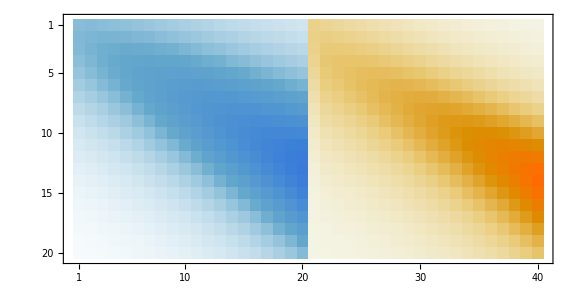
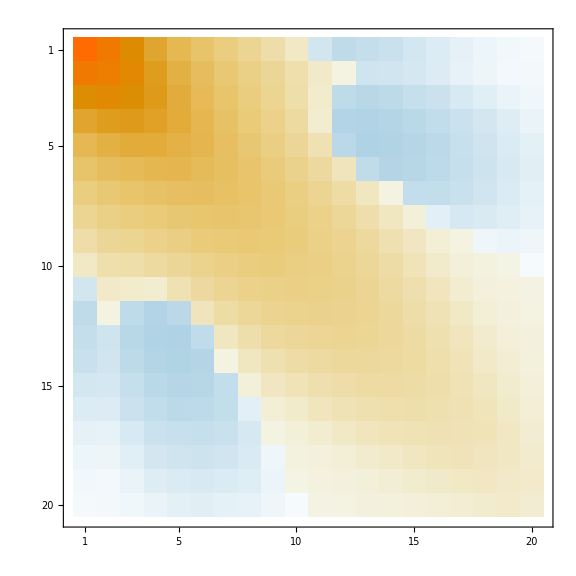
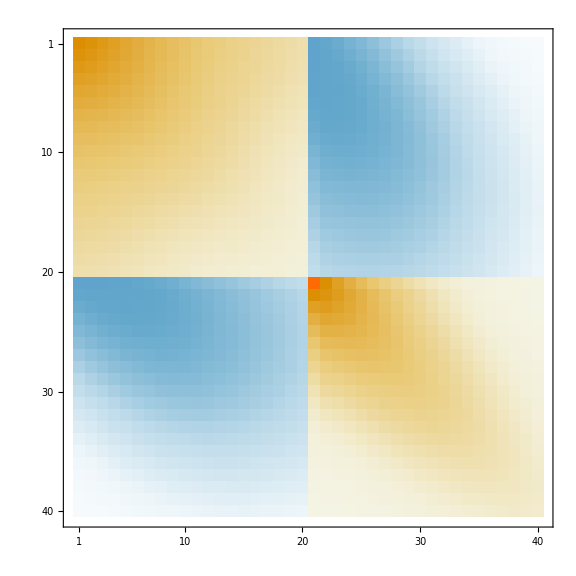
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
nb=1;nj=1;
Grid[{{
MatrixPlot[Chop[CouplingBlockjAs[[nj]][[nb]][[1]][[2]]],FrameLabel->{MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{Optimal Coupling}",Magnification->2],ImageSize->Large]
},{
MatrixPlot[Chop[FSHam[[nj]][[nb]]],FrameLabel->{MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{Final-state Hamiltonian}",Magnification->2],ImageSize->Large]
,
MatrixPlot[Chop[DHam],FrameLabel->{MaTeX["{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{D Hamiltonian}",Magnification->2],ImageSize->Large]
}}]
```

#### Analysis of RHS

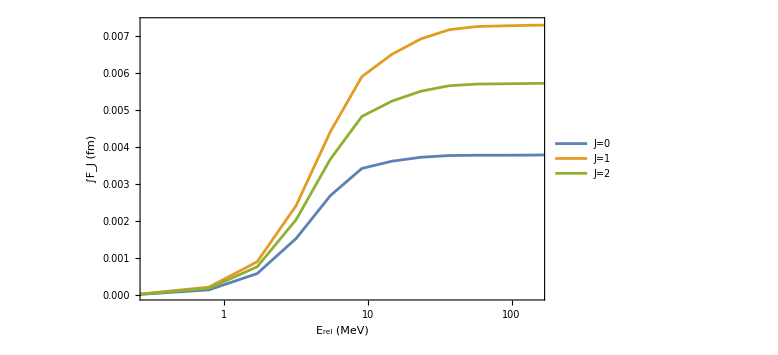

/tmp/strengthF-5-86787.dat

```mathematica
inhomoEBp=Table[{},{nj,Length[Subscript[I, n]]}];
inhomoEB=Table[{},{nj,Length[Subscript[I, n]]}];
Do[(* final-state-J loop *)
Do[(* basis-scenario loop *)
Do[(* Subscript[m, L] loop *)
tmpt=Transpose[fulltrafosαβ[[nj]][[nb]]].CouplingBlockjAs[[nj]][[nb]][[mm]][[2]].fulltrafonm;
tmpf=Table[{
esysFS[[nj]][[nb]][[nfs]][[1]],
αfine/1.0 (esysFS[[nj]][[nb]][[nfs]][[2]].tmpt.evecGS)^2
},{nfs,1,FSDim}];

AppendTo[inhomoEB[[nj]],tmpf];

,{mm,Range[1,Length[mIns[[nj]]]]}
];
,{nb,Range[anzBas]}
];
,{nj,Range[1,Length[Subscript[I, n]]]}
];

fns=Table[Transpose[{inhomoEB[[Inn]][[1]][[All,1]],Accumulate[inhomoEB[[Inn]][[1]][[All,2]]]}],{Inn,Range[1,Length[Subscript[I, n]]]}];
ListLogLinearPlot[fns,PlotRange->{{0,150},All},ImageSize->Large,Frame->True,PlotRangePadding->0,FrameLabel->{"E_rel (MeV)","∫F_J (fm)"},LabelStyle->Large,Joined->True,PlotLegends->{"J=0","J=1","J=2"}]
outF="/tmp/strengthF-"<>StringReplace[DateString["MinuteExact"],"."->"-"]<>".dat"
Put[fns,outF]
```

```mathematica
data={};
SetDirectory["/tmp"];
FileNames["str*"]
Do[
AppendTo[data,Get[fn]];
,{fn,FileNames["str*"]}]
ListLogLinearPlot[Flatten[data,1],PlotRange->{{0,150},All},ImageSize->Large,Frame->True,PlotRangePadding->0,FrameLabel->{"E_rel (MeV)","∫F_J (fm)"},LabelStyle->Large,Joined->True,PlotLegends->{"J=0","J=1","J=2"}]
```

{strengthF-5-86787.dat}

-Graphics-

```mathematica
asdf={{271195.9446029681,0.004033196439266016},{270645.9930266586,0.007298632628042161},{1.3064238821697675*^6,0.005992458152531702}}
```

{{271196.,0.0040332},{270646.,0.00729863},{1.30642×10^6,0.00599246}}

```mathematica
Last/@fns/asdf
```

{{0.0211046,0.951957},{0.0211475,1.00594},{0.00438104,0.963231}}